```mathematica
(* Copy these commands into your own notebook. *)
```

```mathematica
Pendulum[{θ0_,ω0_},tmax_]:=
Module[{θ},
θ/.First[
NDSolve[{
θ''[t]==-Sin[θ[t]],
θ[0]==θ0,
θ'[0]==ω0},
θ,{t,0,tmax}]
]]
```

```mathematica
DDPendulum[{θ0_,ω0_},tmax_]:=
Module[{θ},
θ/.First[
NDSolve[{
θ''[t]==-Sin[θ[t]]-0.05θ'[t]+2.5Sin[t],
θ[0]==θ0,
θ'[0]==ω0},
θ,{t,0,tmax}]
]]
```

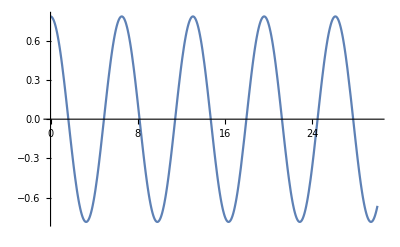

```mathematica
(* Example use. *)
f =Pendulum[{π/4,0},30];
Plot[f[t],{t,0,30}]
```

```mathematica
(* Don't use values for t greater than tmax. *)
f = Pendulum[{π/4,0},30];
f[40]
```

InterpolatingFunction::dmval: Input value {40} lies outside the range of data in the interpolating function. Extrapolation will be used.

699.701